Data Types

```mathematica
a=1;
b=2.7;
c="c";
d={1,2,3.5};
e=<|1->"a",2->"b",3->"γ","3.5"->"d"|>;
vars={a,b,c,d,e};
```

```mathematica
d[[2]] (* Indices in Mathematica start at 1 (in contrast to Python, where they start at zero)*)
e[["3.5"]]
```

2

d

```mathematica
Print[e]
e//Print (*Postfix notation: Apply function (here "Print" to the argument (here "e"))*)
```

<|1→a,2→b,3→γ,3.5→d|>

<|1→a,2→b,3→γ,3.5→d|>

```mathematica
Print=7 (*Mathematica protects its built-in symbols*)
```

Set::wrsym: Symbol Print is Protected.

7

Loops and Conditionals

```mathematica
For[i=1,i<=Length[vars], i++,
Print["Index ", i, " of vars has value ", vars[[i]]];
];
```

Index 1 of vars has value 1

Index 2 of vars has value 2.7

Index 3 of vars has value c

Index 4 of vars has value {1,2,3.5}

Index 5 of vars has value <|1→a,2→b,3→γ,3.5→d|>

Map is similar to the star operator in python, it applies an array as arguments to the function
Thread is very similar to Map. In simple cases they do the same thing (see below), but can do slightly different, more complicated things
Apply uses an array as function inputs, this is like the “star operator” in Python

```mathematica
Map[f,{x,y,z}]
f/@{x,y,z} (*Shorthand for Map*)
Thread[f[{x,y,z}]]
Apply[f,{x,y,z}]
f@@{x,y,z} (*Shorthand for Apply*)
(*Examples*)
Log/@Range[10]//N
Plus@@Range[10]
```

{f[x],f[y],f[z]}

{f[x],f[y],f[z]}

{f[x],f[y],f[z]}

f[x,y,z]

f[x,y,z]

{0.,0.693147,1.09861,1.38629,1.60944,1.79176,1.94591,2.07944,2.19722,2.30259}

55

```mathematica
(*Th start a python Line, simply type ">"*)
```

from math import log
map(log, list(range(1, 11)))

{0.,0.693147,1.09861,1.38629,1.60944,1.79176,1.94591,2.07944,2.19722,2.30259}

print(*range(1, 11))

1 2 3 4 5 6 7 8 9 10

In a more functorial programming way, we can map the elements of vars to the print function .

```mathematica
MapThread[Print["Index ", #1, " of vars has value ", #2]&,{Range[Length[vars]],vars}];
```

Index 1 of vars has value 1

Index 2 of vars has value 2.7

Index 3 of vars has value c

Index 4 of vars has value {1,2,3.5}

Index 5 of vars has value <|1→a,2→b,3→γ,3.5→d|>

Here, the # & serves to define a temporary function, similar to lambda in python

```mathematica
Print[#]&/@Range[Length[vars]]
```

1

2

3

4

5

{Null,Null,Null,Null,Null}

map(lambda x: print(x + 1), range(5));

1

2

3

4

5

{Null,Null,Null,Null,Null}

Plotting

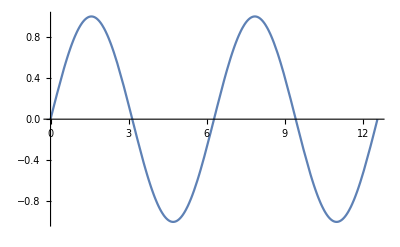

```mathematica
Plot[Sin[x],{x,0,4π}]
```

```mathematica
Plot3D[Sin[x]Cos[y],{x,0,4π},{y,0,4π}]
```

-Graphics3D-

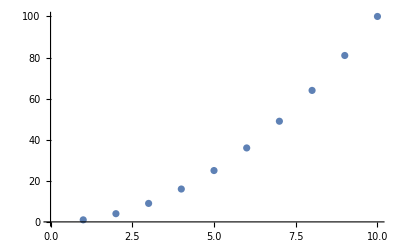

```mathematica
ListPlot[Table[x^2,{x,10}]]
```

```mathematica
p1=ListPointPlot3D[Table[x^2 Log[y],{y,10},{x,10}]]
p2=Plot3D[x^2 Log[y],{x,1,10},{y,1,10}]
Show[p1,p2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

Differentiation and Integration

```mathematica
D[Sin[x],x]//Simplify
Integrate[Sin[x],x]//Simplify
```

Cos[x]

-Cos[x]

Substitution of symbols

```mathematica
Sin[x]/.{x->y}
Sin[x]/.{x->π/4}
Table[Sin[x]/.{x:>If[x>π, -x,x]},{x,0,2π,2π/10}]
```

Sin[y]

1/(√2)

{0,√(5/8-(√5)/8),√(5/8+(√5)/8),√(5/8+(√5)/8),√(5/8-(√5)/8),0,-√(5/8-(√5)/8),-√(5/8+(√5)/8),-√(5/8+(√5)/8),-√(5/8-(√5)/8),0}